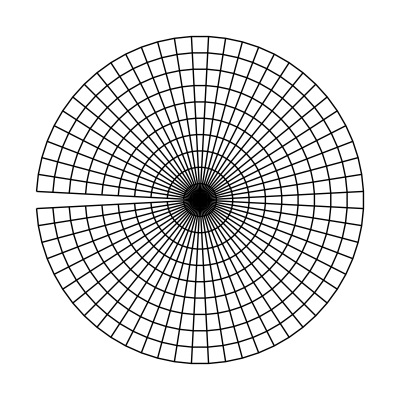

```mathematica
dphi=Pi/30;
rend=0.99;
pts=Table[r*Exp[I N[phi,30]],{phi,-Pi+dphi/2,Pi-dphi/2,dphi},{r,0,rend,rend/10}];

toColor[z_]:=List@@ColorConvert[Hue[Arg[N[z]]/(2 Pi)],"RGB"]
line[pts_]:=line[pts,Identity];
line[pts_,func_]:=Line[ReIm[func[pts]],VertexColors->(toColor/@pts)]
Graphics[{line/@pts,line/@Transpose[pts]}]
g[z_]:=(I-z)/(I+z);
g1[z_]:=InverseFunction[g][z];
F[z_]:=g[Log[g1[z]]/Pi];
cF=Compile[{{z,_Complex,0}},#,Parallelization->True,RuntimeAttributes->{Listable}]&[F[z]]
Graphics[{Gray,Circle[{-.5,0},.5],Circle[],Thick,Black,line[#,cF]&/@pts,line[#,cF]&/@Transpose[pts],Circle[{Mean[{-1,1/3}],0},4/6]}]
g[z_]:=(I-z)/(I+z);
g1[z_]:=InverseFunction[g][z];
F[z_]:=g[Log[g1[z]]/Pi];
F2[z_]:=ReIm@F[Erf[z]];
```

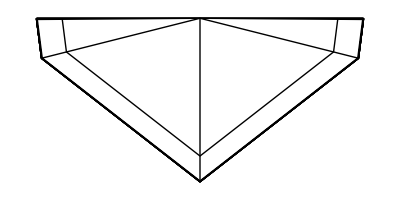

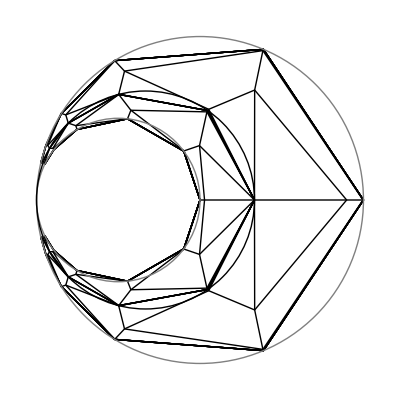

```mathematica
plotPointsPhi=10;
plotPointsR=10;
phiEnd=5;
rend=10;
pts=Table[Erf[r]*Exp[I (Pi/2*Erf[phi]-Pi/2)],{phi,-phiEnd,phiEnd,2 phiEnd/plotPointsPhi},{r,0,rend,rend/plotPointsR}];
oColor[z_]:=List@@ColorConvert[Hue[Arg[N[z]]/(2 Pi)],"RGB"]
ClearAll[line];
line[pts_]:=line[pts,Identity];
line[pts_,func_]:=Line[ReIm[N[func[pts],30]],VertexColors->(toColor/@pts)]
Graphics[{line/@pts,line/@Transpose[pts]}]
Graphics[{line[#,F]&/@pts,line[#,F]&/@Transpose[pts],line[#,F]&/@Conjugate[pts],line[#,F]&/@Conjugate[Transpose[pts]],Thick,Gray,Circle[{-.5,0},.5],Circle[],Black,Circle[{Mean[{-1,1/3}],0},4/6]}]
```

```mathematica
g[z_]:=(I-z)/(I+z);
g1[z_]:=InverseFunction[g][z];
F[z_]:=g[Log[g1[z]]/Pi];
cF=Compile[{{z,_Complex,0}},#,Parallelization->True,RuntimeAttributes->{Listable}]&[F[z]]
```

CompiledFunction[…]

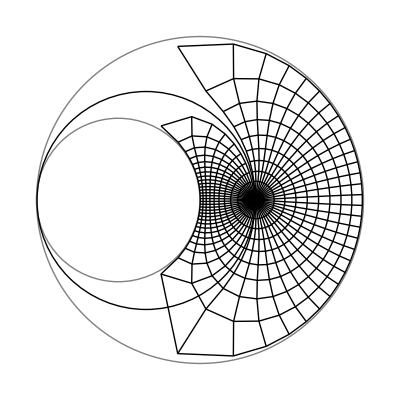

```mathematica
Graphics[{Gray,Circle[{-.5,0},.5],Circle[],Thick,Black,line[#,cF]&/@pts,line[#,cF]&/@Transpose[pts],Circle[{Mean[{-1,1/3}],0},4/6]}]
```

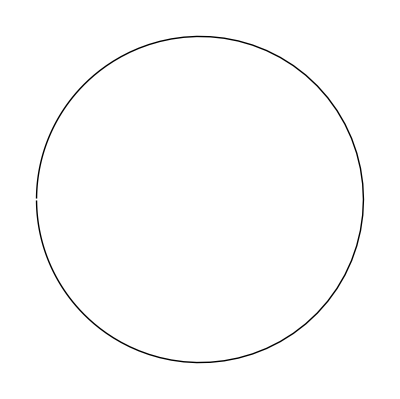

```mathematica
g[z_]:=(I-z)/(I+z);
g1[z_]:=InverseFunction[g][z];
F[z_]:=g[Log[g1[z]]/Pi];
F2[z_]:=ReIm@F[Erf[z]];

$MaxExtraPrecision=1000;
circ=F2/@Range[-40,40,1/10];
Graphics[Line[N[circ,300]]]
```

```mathematica
plotPointsPhi=10;
plotPointsR=10;
phiEnd=5;
rend=10;
pts=Table[Erf[r]*Exp[I (Pi/2*Erf[phi]-Pi/2)],{phi,-phiEnd,phiEnd,2 phiEnd/plotPointsPhi},{r,0,rend,rend/plotPointsR}];
oColor[z_]:=List@@ColorConvert[Hue[Arg[N[z]]/(2 Pi)],"RGB"]
ClearAll[line];
line[pts_]:=line[pts,Identity];
line[pts_,func_]:=Line[ReIm[N[func[pts],30]],VertexColors->(toColor/@pts)]
Graphics[{line/@pts,line/@Transpose[pts]}]
Graphics[{line[#,F]&/@pts,line[#,F]&/@Transpose[pts],line[#,F]&/@Conjugate[pts],line[#,F]&/@Conjugate[Transpose[pts]],Thick,Gray,Circle[{-.5,0},.5],Circle[],Black,Circle[{Mean[{-1,1/3}],0},4/6]}]
```

-Graphics-

-Graphics-

```mathematica
Manipulate[Clear[x,ft];
x[t_,omega_]:=Sin[t] Cos[omega t];
ft[f_,omega_]:=Evaluate[FourierTransform[x[t,omega],t,f,FourierParameters->{1,-1}]];
GraphicsRow[{Plot[x[t,omega],{t,-Pi,Pi},PlotLabel->"x(t)",AxesLabel->{"t","x(t)"}],Plot[Evaluate[Abs[ft[f,omega]]],{f,-5,5},PlotLabel->"|X(f)|",AxesLabel->{"f","|X(f)|"},PlotRange->All]}],{omega,-Pi/2,Pi/2}]
```